{1.87648,38.013,25.4509,4.51296,0.167731,1.72004,26.3411,26.768,0,0.,0}

{67.2623,28.6973,32.6298,66.9518,91.9761,77.0867,38.6498,32.4716,72.7111,83.3526,75.6372}

{30.8612,33.2898,41.9193,28.5353,7.85618,21.1933,35.009,40.7604,27.2889,16.6474,24.3628}

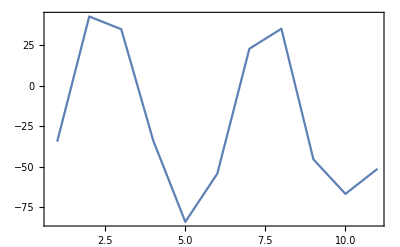

```mathematica
twobright = {1.8764766960404653,38.01295755128127,25.450860943816462,4.512963948785171,0.16773122387746467,1.7200379624799291,26.34112490278458,26.768019649375102,0,0.0,0}
onebright = {67.26233527255602,28.697285024527154,32.6298240318637,66.95177755291817,91.97608805089082,77.0866597454336,38.64982814669785,32.47161661802742,72.71106448976286,83.3525730593354,75.63718407685187}
nobright = {30.861188031403515,33.28975742419158,41.919315024319836,28.535258498296656,7.8561807252317095,21.19330229208647,35.00904695051758,40.760363732597476,27.28893551023714,16.6474269406646,24.362815923148133}

ListLinePlot[(twobright + nobright - onebright), PlotRange -> All, Frame-> True]
```

```mathematica
brightlistone = {120,229,253,336,341,308,255,157,92,73,79};
brightlisttwo ={138,83,51,44,48,62,78,117,158,151,141};
brightlistzero = 400 - brightlistone - brightlisttwo;
errm2 = {{0.978,0.022,0.0},{0.024,0.8539999999999999,0.122},{0.002,0.226,0.7720000000000002}};
probzero = Table[brightlistzero⟦i⟧ errm2⟦1⟧⟦1⟧, {i, 1, Length[brightlistone]}]
```

## ASYM12 scan

```mathematica
ydat = {0.6394938541727447,0.5441178887013599,0.3637822967288869,0.17318008733775322,0.041895942980109256,5.129749545203968*^-10,0.02847665879641199,0.07818235196428534,0.10369875704975774,0.0898445998282373,0.05474294614517005,0.03020287700018574};
δdet = -200;
δstep = 40;
xdat = Table[δdet + i δstep,{i, 0, 11}];
data = Transpose[{xdat, ydat}];
```

0.00666093-0.000105667 x+0.0000194191 x^2-8.4225×10^-8 x^3-2.74009×10^-10 x^4+1.26044×10^-12 x^5

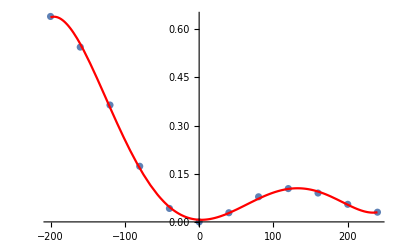

```mathematica
curvefit = Fit[data, {1, x, x^2, x^3, x^4, x^5}, {x}]
Show[ListPlot[data], 
	Plot[curvefit, {x, -200, 240}, PlotStyle -> {Red}]]
```

## ASYM1 scan

```mathematica
ydat = {0.3973142753031997,0.2591183163453215,0.14283092949090415,0.059888869900974126,0.013610914771003417,5.129749545163796*^-10,0.010103375179437562,0.03309607198581618,0.059169633211692226,0.08149602173813872,0.09691227115405024,0.10540163802510776};
δdet = -200;
δstep = 40;
xdat = Table[δdet + i δstep,{i, 0, 11}];
data = Transpose[{xdat, ydat}];
```

-0.000212919-0.0000138263 x+7.53256×10^-6 x^2-2.56263×10^-8 x^3-3.39344×10^-11 x^4+1.78523×10^-13 x^5

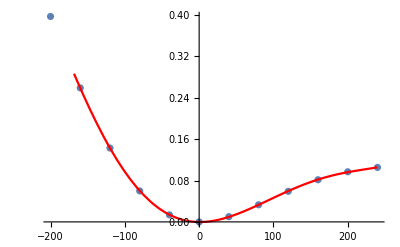

```mathematica
curvefit = Fit[data, {1, x, x^2, x^3, x^4, x^5}, {x}]
Show[ListPlot[data], 
	Plot[curvefit, {x, -200, 240}, PlotStyle -> {Red}]]
```

## -ASYM12 scan

```mathematica
ydat = {0.32420672201441136,0.2556767574007566,0.17043304087772218,0.08581682693922468,0.02315552470583268,5.686943311620009*^-6,0.02315552470583273,0.08581682693922464,0.17043304087772204,0.2556767574007563,0.3242067220144109,0.36772245812426707}
δdet = -200;
δstep = 40;
xdat = Table[δdet + i δstep,{i, 0, 11}];
data = Transpose[{xdat, ydat}];
```

{0.324207,0.255677,0.170433,0.0858168,0.0231555,5.68694×10^-6,0.0231555,0.0858168,0.170433,0.255677,0.324207,0.367722}

0.00355201+0.0000531236 x+0.0000132693 x^2-6.15207×10^-9 x^3-1.3053×10^-10 x^4+1.3014×10^-13 x^5

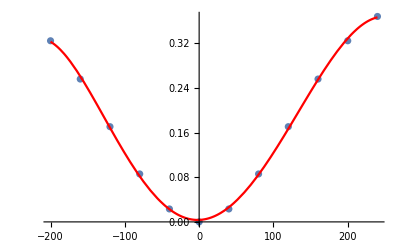

```mathematica
curvefit = Fit[data, {1, x, x^2, x^3, x^4, x^5}, {x}]
Show[ListPlot[data], 
	Plot[curvefit, {x, -200, 240}, PlotStyle -> {Red}]]
```

## SYM scan

```mathematica
ydatdark = {0.62860213095065,0.6346661171535878,0.6357716798812486,0.6223658411244145,0.5812072631385563,0.4999999592189946,0.37999671738196766,0.24955961618368486,0.1566130597898227,0.1329650680187715,0.168614083116214,0.2277826909419088};
ydatbright = {0.23015190041687547,0.24269366687205687,0.2708770461778269,0.3223745286350014,0.4010967253506077,0.49999981850047953,0.597252174482969,0.6642266403475554,0.6821310909239428,0.6518715584835598,0.5912556760652516,0.5243073988364177}
δdet = -200;
δstep = 40;
xdat = Table[δdet + i δstep,{i, 0, 11}];
datadark = Transpose[{xdat, ydatdark}];
databright = Transpose[{xdat, ydatbright}];
```

{0.230152,0.242694,0.270877,0.322375,0.401097,0.5,0.597252,0.664227,0.682131,0.651872,0.591256,0.524307}

0.48959-0.00275541 x-8.00672×10^-6 x^2+6.35473×10^-8 x^3+1.41682×10^-10 x^4-6.07823×10^-13 x^5

0.501997+0.00250148 x-1.53875×10^-6 x^2-6.1406×10^-8 x^3-1.95031×10^-11 x^4+5.33382×10^-13 x^5

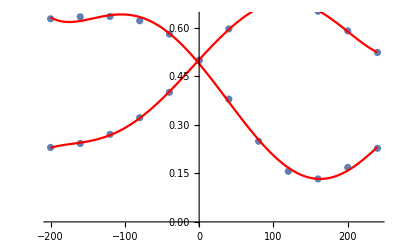

```mathematica
curvefitdark = Fit[datadark, {1, x, x^2, x^3, x^4, x^5}, {x}]
curvefitbright = Fit[databright, {1, x, x^2, x^3, x^4, x^5}, {x}]
Show[ListPlot[datadark], ListPlot[databright], 
	Plot[{curvefitdark, curvefitbright}, {x, -200, 240}, PlotStyle -> {Red}]]
```